```mathematica
SetDirectory[NotebookDirectory[]];
Get["../src/ReactionKinetics.wl"];
Get["../src/ReactionKinetics.wl"];
```

ReactionKinetics Version 1.0 [March 25, 2018] using Mathematica Version 13.0.0 for Linux x86 (64-bit) (December 3, 2021) (Version 13., Release 0) loaded 17 January 2023 at 04:49 TimeZone
GNU General Public License (GPLv3) Terms Apply.

Please report any issues, comments, complaint related to ReactionKinetics at
[jtoth@math.bme.hu](mailto:jtoth@math.bme.hu), [nagyal@math.bme.hu](mailto:nagyal@math.bme.hu) or [dpapp@iems.northwestern.edu](mailto:dpapp@iems.northwestern.edu)

ReactionKinetics Version 1.0 [March 25, 2018] using Mathematica Version 13.0.0 for Linux x86 (64-bit) (December 3, 2021) (Version 13., Release 0) loaded 17 January 2023 at 04:49 TimeZone
GNU General Public License (GPLv3) Terms Apply.

Please report any issues, comments, complaint related to ReactionKinetics at
[jtoth@math.bme.hu](mailto:jtoth@math.bme.hu), [nagyal@math.bme.hu](mailto:nagyal@math.bme.hu) or [dpapp@iems.northwestern.edu](mailto:dpapp@iems.northwestern.edu)

## ReactionsData

ReactionsData[{}]["Properties"]
	Returns all the properties calculated by ReactionsData

ReactionsData[{r_1,r_2,...}][prop]
	Returns the property prop of the reaction network given by {r_1,r_2,...}

ReactionsData[{r_1,r_2,...}][prop1,prop2,...]
	Returns properties {prop1,prop2,...} of the reaction network given by {r_1,r_2,...}

ReactionsData[{r_1,r_2,...}]
	Returns all properties of the reaction network given by {r_1,r_2,...} as a dispatch table

### Examples

#### Basic examples

```mathematica
ReactionsData[{}]["Properties"]
```

{species,M,externalspecies,E,reactionsteps,R,complexes,fhjgraphedges,fhjweaklyconnectedcomponents,fhjstronglyconnectedcomponents,fhjterminalstronglyconnectedcomponents,N,L,S,deficiency,α,β,γ,reactionsteporders,variables,volpertgraph}

```mathematica
model={"A"->"B",2"B"<->"C"};
```

```mathematica
ReactionsData[model]["species"]
```

{X,Y,Z}

```mathematica
ReactionsData[model]["species","complexes", "deficiency"]
```

{{X,Y,Z},{X+Y,2 Y,Y+Z,2 Z,X+Z,2 X},δ=N-L-S=6-3-2=1}

#### Options

##### ExternalSpecies & InternalSpecies

External species can be specified by ExternalSpecies or InternalSpecies. External species have constant concentrations.

```mathematica
ReactionsData[GetReaction["Lotka"]]["reactionsteps"]
```

{A→X,X+Y→2 Y,Y→P}

```mathematica
ReactionsData[GetReaction["Lotka"], ExternalSpecies->{"P"}]["fhjgraphedges"]
```

{A→X,X+Y→2 Y,Y→0}

```mathematica
ReactionsData[GetReaction["Lotka"], InternalSpecies->{"A","X","Y"}]["fhjgraphedges"]
```

{A→X,X+Y→2 Y,Y→0}

#### Properties & Relations

Nearly all functions accepting list of reactions as inputs uses ReactionsData to process it. Its ExternalSpecies & InternalSpecies are applicable everywhere.

## ShowFHJGraph

FHJGraph[{r_1,r_2,...}]
	Draws the Feinberg-Horn-Jackson graph of the reaction network given by {r_1,r_2,...}

FHJGraph[{r_1,r_2,...,r_n},{k_1,k_2,...,k_n}]
	Draws the Feinberg-Horn-Jackson graph of the reaction network given by {r_1,r_2,...} with reaction rates {k_1,k_2,...,k_n}

### Examples

#### Basic examples

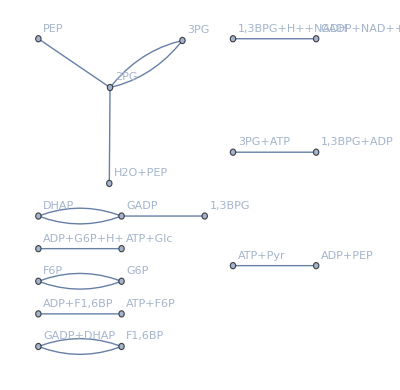

```mathematica
ShowFHJGraph[GetReaction["Glycolysis"],VertexLabels->"Name"]
```

#### Options

##### ExternalSpecies & InternalSpecies

External species can be specified by ExternalSpecies or InternalSpecies. External species have constant concentrations.

```mathematica
ReactionsData[GetReaction["Lotka"], ExternalSpecies->{"P"}]["fhjgraphedges"]
```

{A→X,X+Y→2 Y,Y→0}

```mathematica
ReactionsData[GetReaction["Lotka"], InternalSpecies->{"A","X","Y"}]["fhjgraphedges"]
```

{A→X,X+Y→2 Y,Y→0}

##### GraphFunction

ShowFHJGraph accepts plot functions GraphPlot, LayeredGraphPlot, GraphPlot3D, TreePlot with all of their options

```mathematica
ShowFHJGraph[GetReaction["Lotka"],{1,2,3},PlotFunction->"GraphPlot3D", VertexLabels->"Name"]
```

-Graphics3D-

##### ComplexColors

The complex labels can be colored by ComplexColors

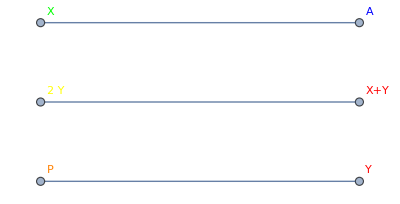

```mathematica
ShowFHJGraph[GetReaction["Lotka"],ComplexColors->{Blue, Green, Red, Yellow, Red, Orange},VertexLabels->"Name"]
```

##### StronglyConnectedComponentColors

The colors of strongly connected components of the FHJ graph can be set by together by StronglyConnectedComponentColors

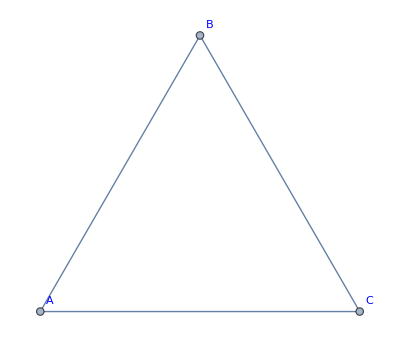

```mathematica
ShowFHJGraph[GetReaction["Triangle"],StronglyConnectedComponentsColors->{Blue},VertexLabels->"Name"]
```

#### Properties & Relations

Uses ReactionsData to process the reaction list. Its options are usable with ShowFHJGraph.

## ShowVolpertGraph

ShowVolpertGraph[{r_1,r_2,...},{s_1,s_2,...}]
	Draws the Volpert graph of the reaction network given by {r_1,r_2,...} starting from species {s_1,s_2,...}

### Examples

#### Basic examples

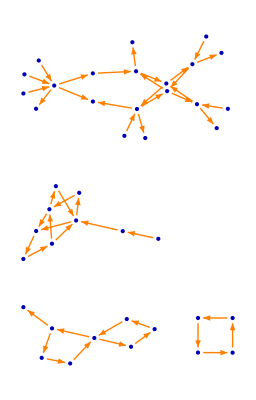

```mathematica
ShowVolpertGraph[GetReaction["Glycolysis"]]
```

#### Options

##### Highlighted

Volpert graphs can be quite large and hard to read. ShowVolpertGraph can highlight parts of it.

```mathematica
species=ReactionsData[GetReaction["Glycolysis"]]["species"]
```

{ATP,Glc,ADP,G6P,H+,G6P,F6P,F6P,F1,6BP,F1,6BP,DHAP,GADP,GADP,NAD+,Pi,1,3BPG,NADH,1,3BPG,3PG,2PG,3PG,H2O,PEP,PEP,Pyr}

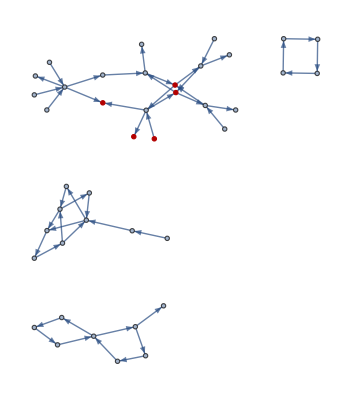

```mathematica
ShowVolpertGraph[GetReaction["Glycolysis"], Highlighted->species[[1;;5]]]
```

##### Indexed

The start of  Volpert indexing can be specified by the Indexed option

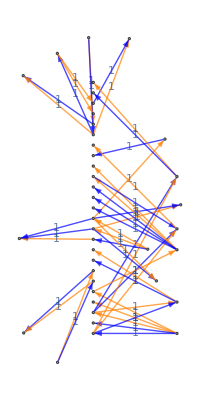

```mathematica
species=ReactionsData[GetReaction["Glycolysis"]]["species"];
ShowVolpertGraph[GetReaction["Glycolysis"], Indexed->species[[1;;5]]]
```

##### Numbered

The Volpert indices can be shown by the Numbered option

```mathematica
ShowVolpertGraph[GetReaction["Glycolysis"], Numbered->True]
```

-Graphics-

#### Properties & Relations

Uses ReactionsData to process the reaction list. Its options are usable with ShowVolpertGraph.

## ShowSCLGraph

ShowSCLGraph[{r_1,r_2,...}]
	Draws the spcies-complex-linkage class graph of the reaction netwrok given by {r_1,r_2,...}

### Examples

#### Basic examples

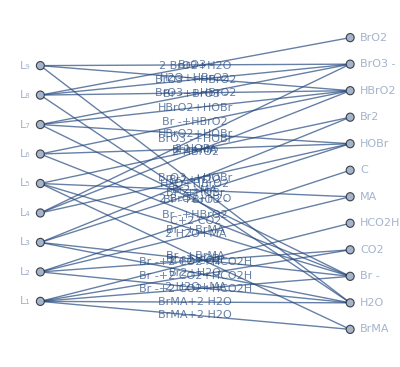

```mathematica
ShowSCLGraph[GetReaction["FKN mechanism"],VertexLabels->"Name"]
```

#### Options

##### GraphPlot

Has all the options of GraphPlot.

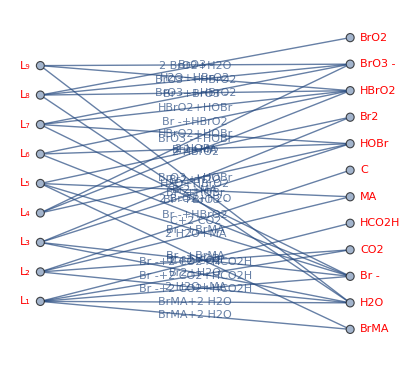

```mathematica
ShowSCLGraph[GetReaction["FKN mechanism"],VertexLabels->"Name",VertexLabelStyle->Red]
```

#### Properties & Relations

Uses ReactionsData to process the reaction list. Its options are usable with ShowSCLGraph. Uses SCLGraph to create the graph then applies BipartiteEmbedding GraphLayout. Use SCLGraph with any graph plot function for finer control over the output.